```mathematica
ϵ=1;
Dp=0.4;
rc=1.5 Dp;
u=2ϵ(1/2 (Dp/r)^4-1)
v=Exp[Dp/(r-rc)+2]
Upatch=u v
```

2 (-1+0.0128/r^4)

ⅇ^(2+0.4/(-0.6+r))

2 ⅇ^(2+0.4/(-0.6+r)) (-1+0.0128/r^4)

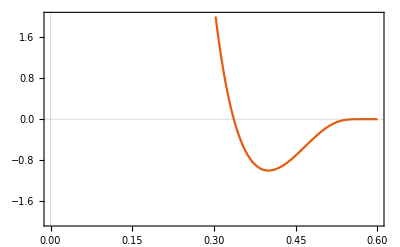

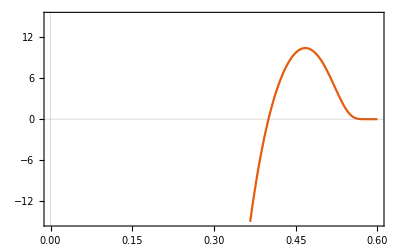

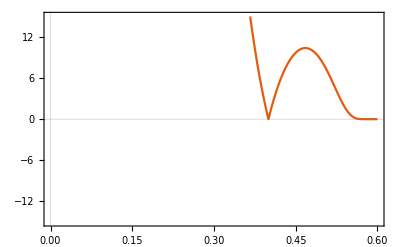

-Graphics-

-Graphics-

```mathematica
Plot[Upatch/.r->x,{x,0,rc},PlotRange->2,PlotTheme->"Scientific"]
Plot[D[Upatch,r]/.r->x,{x,0,rc},PlotRange->15,PlotTheme->"Scientific"]
Plot[Abs[D[Upatch,r]]/.r->x,{x,0,rc},PlotRange->15,PlotTheme->"Scientific"]
```

```mathematica
ClearAll[ϵ,Dp,rc]
u=2ϵ(1/2 (Dp/r)^4-1)
v=Exp[Dp/(r-rc)+2]
Upatch=u v

up=D[u,r]
vp=D[v,r]

up v + u vp

D[Upatch,r]
D[Upatch,r]/.u->s
```

2 (-1+Dp^4/(2 r^4)) ϵ

ⅇ^(2+Dp/(r-rc))

2 ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ

-(4 Dp^4 ϵ)/r^5

-(Dp ⅇ^(2+Dp/(r-rc)))/(r-rc)^2

-(4 Dp^4 ⅇ^(2+Dp/(r-rc)) ϵ)/r^5-(2 Dp ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ)/(r-rc)^2

-(4 Dp^4 ⅇ^(2+Dp/(r-rc)) ϵ)/r^5-(2 Dp ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ)/(r-rc)^2

-(4 Dp^4 ⅇ^(2+Dp/(r-rc)) ϵ)/r^5-(2 Dp ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ)/(r-rc)^2

```mathematica
up
u
```

-(4 Dp^4 ϵ)/r^5

2 (-1+Dp^4/(2 r^4)) ϵ

```mathematica
Simplify[2 (-1+Dp^4/(2 r^4)) ϵ]
```

(-2+Dp^4/r^4) ϵ

```mathematica
Expand[(-2+Dp^4/r^4) ϵ]
```

-2 ϵ+(Dp^4 ϵ)/r^4

```mathematica
dif=up-u
dif2=u-up

FullSimplify[dif2]
(up+dif2)-u //Simplify
u//Simplify
```

-2 (-1+Dp^4/(2 r^4)) ϵ-(4 Dp^4 ϵ)/r^5

2 (-1+Dp^4/(2 r^4)) ϵ+(4 Dp^4 ϵ)/r^5

(-2+(Dp^4 (4+r))/r^5) ϵ

0

(-2+Dp^4/r^4) ϵ

```mathematica
Simplify[2 (-1+Dp^4/(2 r^4)) ϵ+(4 Dp^4 ϵ)/r^5]
```

(-2+(Dp^4 (4+r))/r^5) ϵ

```mathematica
ExpandAll[-2 (-1+Dp^4/(2 r^4)) ϵ-(4 Dp^4 ϵ)/r^5]
```

2 ϵ-(4 Dp^4 ϵ)/r^5-(Dp^4 ϵ)/r^4

```mathematica
Simplify[2 ϵ-(4 Dp^4 ϵ)/r^5-(Dp^4 ϵ)/r^4]
```

(2-(Dp^4 (4+r))/r^5) ϵ

```mathematica
Expand[(-2+Dp^4/r^4) ϵ]
```

-2 ϵ+(Dp^4 ϵ)/r^4